# Rydberg addressing train propogation

P. Huft

All units in mm.

## Gaussian beam params, matrices, functions

```mathematica
MProp[d_]:={{1,d},{0,1}};
MRefract[n1_,n2_,r_]:={{1,0},{(n1-n2)/(n2 r),n1/n2}};
MLens [f_]:= {{1,0},{-1/f,1}};
qM[q_,M_]:= (q M[[1,1]]+M[[1,2]])/(q M[[2,1]]+M[[2,2]]);
wq[q_,z_]:=√(λ/(π Im[1/(q+z)]));
w[z_,w0_]:= w0(1+((z λ)/(π w0^2))^2)^(1/2);
beamPropagate[qInit_,sys_]:=Module[{q=qInit,qNext,lines={},i,element,z=0,zNext},
(*return list of piecewise functions showing beam propagation*)
For[i=1,i≤Length[sys],i++,
element=sys[[i]];
qNext=qM[q,element[[1]]];
zNext=z+element[[2]];
AppendTo[lines,Piecewise[{{wq[qNext,x-z]/10^-3,z<x<zNext}}]];
q=qNext+element[[2]];
z=zNext;
]; (*waist in [m]*)
lines
]

beamPropagatePlot[qInit_,sys_,logplot_:False]:=Module[{q=qInit,qNext,lines={},i,element,z=0,zNext,x},
(*plots the piecewise beam propagation*)
For[i=1,i≤Length[sys],i++,
element=sys[[i]];
qNext=qM[q,element[[1]]];
zNext=z+element[[2]];
AppendTo[lines,Piecewise[{{wq[qNext,x-z]/10^-3,z<x<zNext}}]];
q=qNext+element[[2]];
z=zNext;
]; (*waist in [m]*)
If[logplot,
LogPlot[Evaluate[lines],{x,10*^-4,z},PlotRange->Automatic,Frame->False],
Plot[lines,{x,0,z},PlotRange->{0,All},Frame->False]
](*q after transformation M*)
]
USAFlpmm[group_,element_]:=2^(group+(element-1)/6)//N; (*US Air Force standard resolution [line pair/mm] where a line pair is one bright and one dark line*)
```

## Solve for lens f and/or z

Cavity and beam params, and compound transformations. All distances in [m]

```mathematica
w0 = 0.0005; (*starting waist, measured*)
λ=7.8*^-7;
ng =1.45;(*index of ref. fused silica*)
mt = 6.35*^-3;(*mirror thickness*)
wt =0.005;(*can window thickness*)
gap = 0.03; (*approx distance between window and first cav mirror*)
R = 0.1; (*mirror RoC*)
LCav=0.085; (*cavity length*)
MMirror1 = MRefract[ng,1,R].MProp[mt]. MRefract[1,ng,∞]; (*input mirror*)
MMirror2 = MRefract[ng,1,∞].MProp[mt]. MRefract[1,ng,-R]; (*output mirror*)
MWindow = MRefract[ng,1,∞].MProp[wt]. MRefract[1,ng,∞]; (*flat window*)
q0 = -ⅈ (π w0^2)/λ; (*initial beam parameter*)
wCav = √((λ R)/(2 π));(*approx TEM00 waist to match in cavity*)
qCav = (-ⅈ π)/λ wCav^2;(*q param for beam at cavity waist location*)

zR = (π wCav^2)/λ; (*cavity mode Rayleigh range*)
√(λ/(π Im[1/(qCav +zR)]))/wCav ==√2(*Rayleigh range waist as sanity check*)
```

True

Beam waist and RoC immediately after the first cavity mirror

```mathematica
qIn = qCav - LCav/2; 
"roc after input mirror"
rocIn = 1/Re[1/qIn]
"waist after input mirror"
wIn = √(λ/(π Im[1/(qIn)]))
```

roc after input mirror

-0.101324

waist after input mirror

0.00014623

Set two params, solve for other two. The initial beam is transformed by lens f1, propagates d1, transformed by f2, then propagates d2 to first cavity mirror.

```mathematica
Clear[d1,f1,d2,f2]
d2= .10;
d1= .05;
freeVars ={f1,f2};
zWaist = LCav/2; (*axial waist location, measured from first cav mirror*)
MToCav = MMirror1.MProp[d2].MLens[f2].MProp[d1].MLens[f1];
roc1= FullSimplify[Chop[Refine[ComplexExpand[1/Re[1/qM[q0,MToCav]],freeVars∈Reals]]]] ; (*RoC after first cav mirror*)
wMidCav= FullSimplify[Chop[Refine[√(λ ComplexExpand[1/(π Im[1/qM[q0,MProp[zWaist].MToCav]])]),freeVars∈Reals]]];(*waist at desired target location*)
```

Solve the system

```mathematica
soln=NSolve[{roc1==rocIn,wMidCav==wCav},{f1,f2},Reals,WorkingPrecision->16]
```

{{f1→0.197422438772253,f2→3.66871437518742},{f1→0.264524793670504,f2→0.524098119318297},{f1→0.0286248182339208,f2→0.0186556010224018},{f1→0.027609333215255,f2→0.0195898875235561}}

Numerical check

```mathematica
idx = 1; (*soln to use*)
"RoC after input cav mirror, waist at target location:"
{1/Re[1/qM[q0,MToCav/.soln[[idx]]]],√(λ/(π Im[1/qM[q0,MToCav.MProp[LCav/2]/.soln[[idx]]]]))}
"RoC just before output cav mirror:"
1/Re[1/(qM[q0,MToCav/.soln[[idx]]]+LCav)]
```

RoC after input cav mirror, waist at target location:

{-0.101324,0.000126876}

RoC just before output cav mirror:

0.0929117

## 1064 propagation

see Matt’s thesis for initial train design. r.m. = rough measurement

```mathematica
w0 = 1; (*start with collimated beam after fiber*)
λ780 = 7.802*^-6; (*TODO get exact wavelength*)
qStart =q0 = -ⅈ (π w0^2)/λ;(*initial beam parameter*)
f1 = 6.24;(*C110TME-1064*)
d0 = 25+60; (*r.m. CBD after this*)
d1 =0; (*from CBD to f2: MEASURE*)
f2 = 60;(*AC254-060-C*)
d2 = 95;(*r.m.*)
f3 = 19;(*AC127-019-C*)
d3 = 0; (*DE to f3*)
d4 = 0; (*f3 to f4*)
f4 = 80;(*AC254-080-B*)
d5 = 0; (*f4 to f5*)
f5 =8;(*C240TME-B*)
d6 = 0;(*f5 to f6, including path through DBS*)
f6 = 200;(*AC254-200-B*)
d7 = 
f7 = 23.125;(*JenOptik*)
system={
{{{1,0},{0,1}},d0+d1},
(*{MLens[f1],f1},*)
(*calcite beam displacer*)
{MLens[f2],f2},
{MLens[f3],},
{MLens[f4],},
{MLens[f5],},
{MLens[f6],},
{MLens[f7],} 
};
```

## 780 propagation

## 780 fluorescence imaging

## 480 propagation

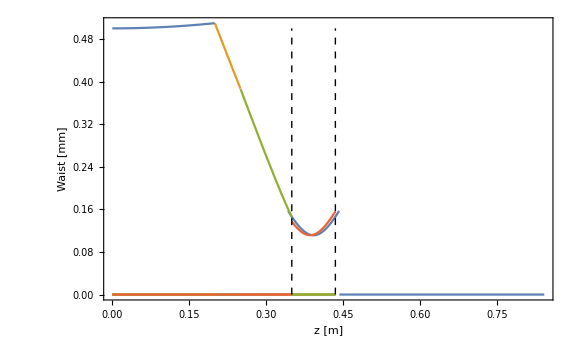

```mathematica
zR=(π wCav^2)/λ;
qStart =q0;
d0=.20; 
dCavity =d0+d1+d2+ LCav/2;
system={
{{{1,0},{0,1}},d0},
{MLens[f1],d1},
{MLens[f2],d2},
{MMirror1,LCav}
}/.soln[[1]];
Show[Plot[Piecewise[{{w[z-dCavity,wCav]/10^-3,dCavity-zR<z <dCavity+zR}}],{z,0,dCavity+zR+0.4},PlotRange->{0,1.1w0/10^-3}],beamPropagatePlot[qStart,system],Graphics[{Dashed,Line[{{dCavity-LCav/2,0},{dCavity-LCav/2,w0/10^-3}}]}],
Graphics[{Dashed,Line[{{dCavity+LCav/2,0},{dCavity+LCav/2,w0/10^-3}}]}],Frame-> {True,True,False,False},Axes-> False,FrameLabel->{"z [m]","Waist [mm]"},ImageSize->Large,PlotRange-> All,LabelStyle-> Directive[Black,FontSize-> 14]]
```

Plot an approximate solution with lenses on hand

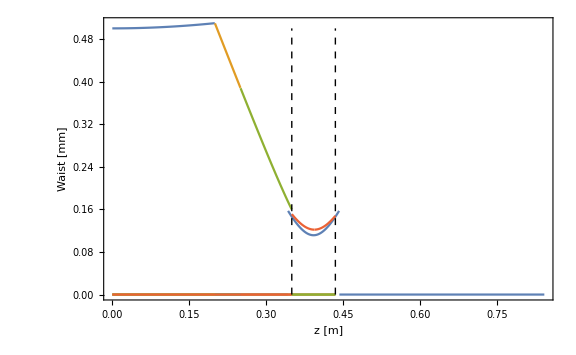

```mathematica
d0=.20; 
dCavity =d0+d1+d2+ LCav/2;
system={
{{{1,0},{0,1}},d0},
{MLens[f1],d1}/.f1-> .2,
{MLens[f2],d2}/.f2->∞,
{MMirror1,LCav}
}/.soln[[1]];
Show[Plot[Piecewise[{{w[z-dCavity,wCav]/10^-3,dCavity-zR<z <dCavity+zR}}],{z,0,dCavity+zR+0.4},PlotRange->{0,1.1w0/10^-3}],beamPropagatePlot[qStart,system],Graphics[{Dashed,Line[{{dCavity-LCav/2,0},{dCavity-LCav/2,w0/10^-3}}]}],
Graphics[{Dashed,Line[{{dCavity+LCav/2,0},{dCavity+LCav/2,w0/10^-3}}]}],Frame-> {True,True,False,False},Axes-> False,FrameLabel->{"z [m]","Waist [mm]"},ImageSize->Large,PlotRange-> All,LabelStyle-> Directive[Black,FontSize-> 14]]
```

```mathematica
d1+d2
```

0.15

## Misc imaging tests

For re-imaging the FORT and Rydberg beams onto a Raspberry Pi camera.

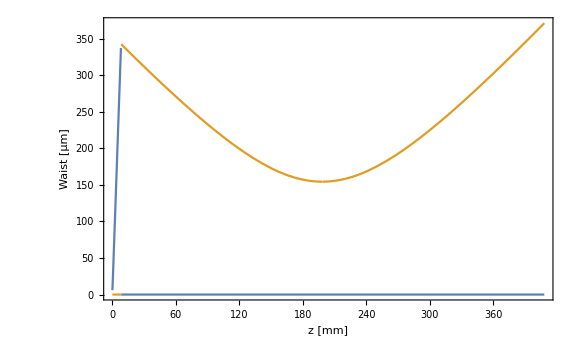

```mathematica
w = 6*^-3; (*x beam waist*)
λ= 7.802*^-4;(*use more accurate wavelength*)
(*w = 2*^-3; 
λ= 10.64*^-4;*)

qStart = -ⅈ (π w^2)/λ;
fAsph = 8;
system = {
{{{1,0},{0,1}},fAsph+.275},
{MLens[fAsph], 400}
};

Show[beamPropagatePlot[qStart,system],Frame-> {True,True,False,False},Axes-> False,FrameLabel->{"z [mm]","Waist [μm]"},ImageSize->Large,PlotRange-> All,LabelStyle-> Directive[Black,FontSize-> 14]]
```

```mathematica
FindMinimum[beamPropagate[qStart,system][[2]],{x,200}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{154.407,{x→198.398}}

```mathematica
FindMinimum[beamPropagate[qStart,system][[2]],{x,250}]
```

{58.1282,{x→248.574}}

Thin lens imaging of DOE standard:

```mathematica
f=8;
d1=8.1;
NSolve[1/f==1/d1+1/d2,d2]
```

{{d2→84.}}

```mathematica
k
```

```mathematica
Solve
```

Plot::plln: Limiting value 1.5 f in {d1,0,1.5 f} is not a machine-sized real number.

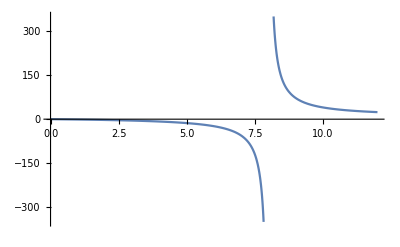

```mathematica
Plot[(f d1)/(d1-f),{d1,0,1.5f},PlotRange->{-350,350}]/.f->8
```

```mathematica
NSolve[(f d1)/(d1-f)==350/.f->8,d1]
```

{{d1→8.18713}}

Magnification = -d2/d1

```mathematica
m=350/8.187134502923977
```

42.75

Test standard group 1,6 lp/mm = 3.56 -> linewidth is 0.14 mm

```mathematica
m*0.14
```

5.985

Magnification is too good.

```mathematica
m*0.002
```

0.0855

```mathematica
1/USAFlpmm[5,6]*m
```

0.74977